```mathematica
Terminals = {x,y,1}
Terminals = Map[Function[{#,0}],Terminals]
(*Functions = {{GPlus,2},{GSubtract,2},{GDivide,2},{GTimes,2},{GExp,1},{GLog,1},{GIdentity,1},{GIncrement,1},{GDecrement,1},{GNegate,1}}*)
Functions = {{GPlus,2},{GSubtract,2},{GDivide,2},{GTimes,2}}
FunctionTranslation={GPlus->Plus,GSubtract->Subtract,GDivide->SafeDivide,GTimes->Times,GExp->SafeExp,GLog->SafeLog,GIdentity->Identity,GIncrement->IncreaseByOne,GDecrement->DecreaseByOne,GNegate->Minus}
DisplayTranslation={GPlus->Plus,GSubtract->Subtract,GDivide->Divide,GTimes->Times,GExp->Exp,GLog->Log,GIdentity->Identity,GIncrement->IncreaseByOne,GDecrement->DecreaseByOne,GNegate->Minus}
SafeDivide[x_,y_]:=If[y==0,1,x/y]
SafeLog[x_]:=If[x==0,1,If[x<0,Log[-x],Log[x]]]
SafeExp[x_]:=Exp[Max[-1.*10^2,Min[1.*10^2,x]]]
IncreaseByOne=#+1&
DecreaseByOne=#-1&
```

{x,y,1}

{{x,0},{y,0},{1,0}}

{{GPlus,2},{GSubtract,2},{GDivide,2},{GTimes,2}}

{GPlus→Plus,GSubtract→Subtract,GDivide→SafeDivide,GTimes→Times,GExp→SafeExp,GLog→SafeLog,GIdentity→Identity,GIncrement→IncreaseByOne,GDecrement→DecreaseByOne,GNegate→Minus}

{GPlus→Plus,GSubtract→Subtract,GDivide→Divide,GTimes→Times,GExp→Exp,GLog→Log,GIdentity→Identity,GIncrement→IncreaseByOne,GDecrement→DecreaseByOne,GNegate→Minus}

#1+1&

#1-1&

```mathematica
TargetFunction[x_,y_]:=x^2 y+x y+y^2+x+x^3 y^2;
DataPoints=Map[Function[{#[[1]],#[[2]],TargetFunction[#[[1]],#[[2]]]}],Table[{RandomReal[{-10,10}],RandomReal[{-10,10}]},{100}]];
```

```mathematica
Show[{ListPlot3D[DataPoints,Mesh->All],Plot3D[TargetFunction[x,y],{x,-10,10},{y,-10,10},Mesh->None]}]
```

-Graphics3D-

```mathematica
TestNode[node_,dataset_]:=Sqrt[Total[Map[Function[pair,TestNodeAtPoint[node,pair]],dataset]]]
TestNodeAtPoint[node_,xypair_]:=
N[(xypair[[3]]-node)^2/.{x->xypair[[1]],y->xypair[[2]]}/.FunctionTranslation]
myTestFunction[node_]:=TestNode[node,DataPoints]
```

```mathematica
myMaxInitDepth=10;
myMaxComplexity=200;
myGenSize=500;
myCrossoverProbability=0.8;
myRegrowProbability=0.2;
myPointProbability=0.1;
myMinSolutionFitness = 0.75;
myFirstGen=Table[CreateTree[myMaxComplexity,myMaxInitDepth],{myGenSize}];
myFirstGenList=Map[NodeToList,myFirstGen];
myCurrentGen=1;
myFirstGenFitness=CalculateFitness[myTestFunction,myFirstGen];
myFirstGenBestPosition=Ordering[myFirstGenFitness,-1][[1]];
myBestFind={myCurrentGen,myFirstGenFitness[[myFirstGenBestPosition]],myFirstGen[[myFirstGenBestPosition]]};
myFirstGen[[myFirstGenBestPosition]]/.DisplayTranslation
Show[ListPlot3D[DataPoints,Mesh->All],Plot3D[(myBestFind[[3]]/.{x->xvar,y->yvar}/.FunctionTranslation),{xvar,-10,10},{yvar,-10,10},Mesh->None]]
```

-x-y+(1+x+y^2) (1-x^2/(1+x+y))

-Graphics3D-

```mathematica
myCurrentGen=1;
myPreviousGenList=myFirstGenList;
myPreviousGenFitness=myFirstGenFitness;
```

Generation = 2

Real = f(x)=x+x y+x^2 y+y^2+x^3 y^2

Best this generation = fitness=7.05674×10^-6 f(x,y)=(2 x^2)/(x+y)+(2 x^2 y)/(x+y)

Best ever = Gen=1 fitness=7.01991×10^-6 f(x,y)=1-y+y^2-x^2/(1+x+y)-x^3/(1+x+y)-(x^2 y^2)/(1+x+y)

Fitnesses =

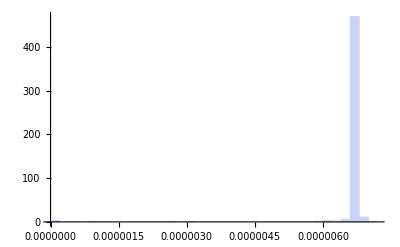

Generation = 3

Real = f(x)=x+x y+x^2 y+y^2+x^3 y^2

Best this generation = fitness=7.1512×10^-6 f(x,y)=-2+(2 x)/y^2-2/y+(2 x)/y+2 y+4 x y+2 y^2+4 x y^2

Best ever = Gen=2 fitness=7.05674×10^-6 f(x,y)=(2 x^2)/(x+y)+(2 x^2 y)/(x+y)

Fitnesses =

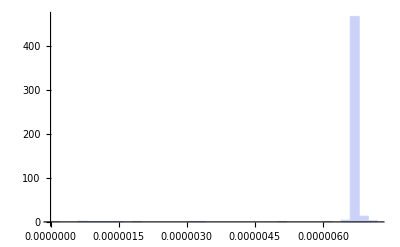

Generation = 4

Real = f(x)=x+x y+x^2 y+y^2+x^3 y^2

Best this generation = fitness=7.1512×10^-6 f(x,y)=-2+(2 x)/y^2-2/y+(2 x)/y+2 y+4 x y+2 y^2+4 x y^2

Best ever = Gen=3 fitness=7.1512×10^-6 f(x,y)=-2+(2 x)/y^2-2/y+(2 x)/y+2 y+4 x y+2 y^2+4 x y^2

Fitnesses =

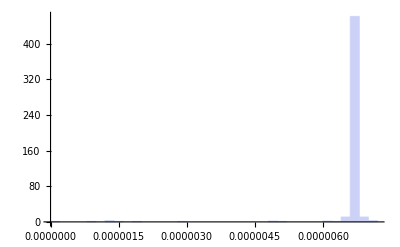

Generation = 5

Real = f(x)=x+x y+x^2 y+y^2+x^3 y^2

Best this generation = fitness=7.38209×10^-6 f(x,y)=1+3 x+4 y+3 x y+y/(1-y)+(3 x y)/(1-y)+4 y^2+6 x y^2+(2 y^2)/(1-y)+4 y^3+y/(-y+(1/2+x) (1+y (x+y)))+y^2/(-y+(1/2+x) (1+y (x+y)))+y^2/((1-y) (-y+(1/2+x) (1+y (x+y))))+(2 y^3)/(-y+(1/2+x) (1+y (x+y)))

Best ever = Gen=3 fitness=7.1512×10^-6 f(x,y)=-2+(2 x)/y^2-2/y+(2 x)/y+2 y+4 x y+2 y^2+4 x y^2

Fitnesses =

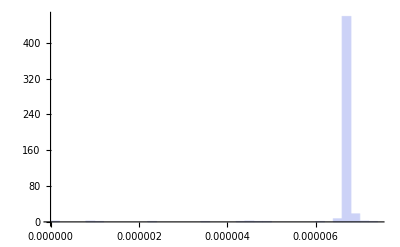

Generation = 6

Real = f(x)=x+x y+x^2 y+y^2+x^3 y^2

Best this generation = fitness=7.38209×10^-6 f(x,y)=1+3 x+4 y+3 x y+y/(1-y)+(3 x y)/(1-y)+4 y^2+6 x y^2+(2 y^2)/(1-y)+4 y^3+y/(-y+(1/2+x) (1+y (x+y)))+y^2/(-y+(1/2+x) (1+y (x+y)))+y^2/((1-y) (-y+(1/2+x) (1+y (x+y))))+(2 y^3)/(-y+(1/2+x) (1+y (x+y)))

Best ever = Gen=5 fitness=7.38209×10^-6 f(x,y)=1+3 x+4 y+3 x y+y/(1-y)+(3 x y)/(1-y)+4 y^2+6 x y^2+(2 y^2)/(1-y)+4 y^3+y/(-y+(1/2+x) (1+y (x+y)))+y^2/(-y+(1/2+x) (1+y (x+y)))+y^2/((1-y) (-y+(1/2+x) (1+y (x+y))))+(2 y^3)/(-y+(1/2+x) (1+y (x+y)))

Fitnesses =

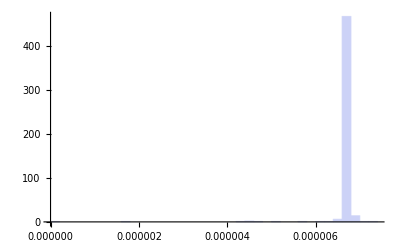

Generation = 7

Real = f(x)=x+x y+x^2 y+y^2+x^3 y^2

Best this generation = fitness=7.81935×10^-6 f(x,y)=-(3 y)/2+y/x+x y+x^2 y-(5 y^2)/2+y^2/x-(3 x y^2)/2+y^3/2+y^3/x-2/(1+y)-1/(2 x^2 (1+y))+7/(4 x (1+y))-(7 x)/(2 (1+y))+x^2/(1+y)+x^3/(1+y)-3/(2 y (1+y))+1/(x y (1+y))+x/(y (1+y))+x^2/(y (1+y))+(23 y)/(4 (1+y))-y/(x^2 (1+y))+y/(x (1+y))-(13 x y)/(2 (1+y))-(5 x^2 y)/(2 (1+y))+(x^3 y)/(1+y)+(23 y^2)/(4 (1+y))-y^2/(2 x^2 (1+y))-(3 y^2)/(4 x (1+y))+(4 x y^2)/(1+y)-(3 x^2 y^2)/(2 (1+y))-(x^3 y^2)/(1+y)-(17 y^3)/(4 (1+y))-(5 y^3)/(2 x (1+y))+(3 x y^3)/(2 (1+y))+(3 x^2 y^3)/(2 (1+y))-y^4/(2 (1+y))+y^4/(2 x^2 (1+y))+(5 y^4)/(4 x (1+y))-(x y^4)/(2 (1+y))+(3 y^2)/(2 (-y+x (-1+x+y)))-y^2/(x (-y+x (-1+x+y)))-(x y^2)/(-y+x (-1+x+y))-(x^2 y^2)/(-y+x (-1+x+y))+(5 y^3)/(2 (-y+x (-1+x+y)))-y^3/(x (-y+x (-1+x+y)))+(3 x y^3)/(2 (-y+x (-1+x+y)))-y^4/(2 (-y+x (-1+x+y)))-y^4/(x (-y+x (-1+x+y)))+3/(2 (1+y) (-y+x (-1+x+y)))-1/(x (1+y) (-y+x (-1+x+y)))-x/((1+y) (-y+x (-1+x+y)))-x^2/((1+y) (-y+x (-1+x+y)))+(2 y)/((1+y) (-y+x (-1+x+y)))+y/(2 x^2 (1+y) (-y+x (-1+x+y)))-(7 y)/(4 x (1+y) (-y+x (-1+x+y)))+(7 x y)/(2 (1+y) (-y+x (-1+x+y)))-(x^2 y)/((1+y) (-y+x (-1+x+y)))-(x^3 y)/((1+y) (-y+x (-1+x+y)))-(23 y^2)/(4 (1+y) (-y+x (-1+x+y)))+y^2/(x^2 (1+y) (-y+x (-1+x+y)))-y^2/(x (1+y) (-y+x (-1+x+y)))+(13 x y^2)/(2 (1+y) (-y+x (-1+x+y)))+(5 x^2 y^2)/(2 (1+y) (-y+x (-1+x+y)))-(x^3 y^2)/((1+y) (-y+x (-1+x+y)))-(23 y^3)/(4 (1+y) (-y+x (-1+x+y)))+y^3/(2 x^2 (1+y) (-y+x (-1+x+y)))+(3 y^3)/(4 x (1+y) (-y+x (-1+x+y)))-(4 x y^3)/((1+y) (-y+x (-1+x+y)))+(3 x^2 y^3)/(2 (1+y) (-y+x (-1+x+y)))+(x^3 y^3)/((1+y) (-y+x (-1+x+y)))+(17 y^4)/(4 (1+y) (-y+x (-1+x+y)))+(5 y^4)/(2 x (1+y) (-y+x (-1+x+y)))-(3 x y^4)/(2 (1+y) (-y+x (-1+x+y)))-(3 x^2 y^4)/(2 (1+y) (-y+x (-1+x+y)))+y^5/(2 (1+y) (-y+x (-1+x+y)))-y^5/(2 x^2 (1+y) (-y+x (-1+x+y)))-(5 y^5)/(4 x (1+y) (-y+x (-1+x+y)))+(x y^5)/(2 (1+y) (-y+x (-1+x+y)))

Best ever = Gen=5 fitness=7.38209×10^-6 f(x,y)=1+3 x+4 y+3 x y+y/(1-y)+(3 x y)/(1-y)+4 y^2+6 x y^2+(2 y^2)/(1-y)+4 y^3+y/(-y+(1/2+x) (1+y (x+y)))+y^2/(-y+(1/2+x) (1+y (x+y)))+y^2/((1-y) (-y+(1/2+x) (1+y (x+y))))+(2 y^3)/(-y+(1/2+x) (1+y (x+y)))

Fitnesses =

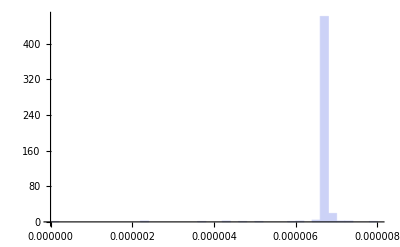

Generation = 8

Real = f(x)=x+x y+x^2 y+y^2+x^3 y^2

Best this generation = fitness=7.49268×10^-6 f(x,y)=-(3 y)/2+y/x+x y+x^2 y-(5 y^2)/2+y^2/x-(3 x y^2)/2+y^3/2+y^3/x-1/(1+y)-1/(2 x^2 (1+y))+7/(4 x (1+y))-(7 x)/(1+y)+(3 x^2)/(1+y)+(3 x^3)/(1+y)-1/(y^2 (1+y))+(3 x)/(2 y^2 (1+y))-x^2/(y^2 (1+y))-x^3/(y^2 (1+y))-5/(2 y (1+y))+1/(x y (1+y))+(7 x)/(2 y (1+y))+(5 x^2)/(2 y (1+y))+(27 y)/(4 (1+y))-y/(x^2 (1+y))+y/(x (1+y))-(10 x y)/(1+y)-(13 x^2 y)/(2 (1+y))+(27 y^2)/(4 (1+y))-y^2/(2 x^2 (1+y))-(3 y^2)/(4 x (1+y))+(15 x y^2)/(2 (1+y))-(x^3 y^2)/(1+y)-(21 y^3)/(4 (1+y))-(5 y^3)/(2 x (1+y))+(x y^3)/(1+y)+(3 x^2 y^3)/(2 (1+y))-y^4/(2 (1+y))+y^4/(2 x^2 (1+y))+(5 y^4)/(4 x (1+y))-(x y^4)/(2 (1+y))+(3 y^2)/(2 (-y+x (-1+x+y)))-y^2/(x (-y+x (-1+x+y)))-(x y^2)/(-y+x (-1+x+y))-(x^2 y^2)/(-y+x (-1+x+y))+(5 y^3)/(2 (-y+x (-1+x+y)))-y^3/(x (-y+x (-1+x+y)))+(3 x y^3)/(2 (-y+x (-1+x+y)))-y^4/(2 (-y+x (-1+x+y)))-y^4/(x (-y+x (-1+x+y)))+5/(2 (1+y) (-y+x (-1+x+y)))-1/(x (1+y) (-y+x (-1+x+y)))-(7 x)/(2 (1+y) (-y+x (-1+x+y)))-(5 x^2)/(2 (1+y) (-y+x (-1+x+y)))+1/(y (1+y) (-y+x (-1+x+y)))-(3 x)/(2 y (1+y) (-y+x (-1+x+y)))+x^2/(y (1+y) (-y+x (-1+x+y)))+x^3/(y (1+y) (-y+x (-1+x+y)))+y/((1+y) (-y+x (-1+x+y)))+y/(2 x^2 (1+y) (-y+x (-1+x+y)))-(7 y)/(4 x (1+y) (-y+x (-1+x+y)))+(7 x y)/((1+y) (-y+x (-1+x+y)))-(3 x^2 y)/((1+y) (-y+x (-1+x+y)))-(3 x^3 y)/((1+y) (-y+x (-1+x+y)))-(27 y^2)/(4 (1+y) (-y+x (-1+x+y)))+y^2/(x^2 (1+y) (-y+x (-1+x+y)))-y^2/(x (1+y) (-y+x (-1+x+y)))+(10 x y^2)/((1+y) (-y+x (-1+x+y)))+(13 x^2 y^2)/(2 (1+y) (-y+x (-1+x+y)))-(27 y^3)/(4 (1+y) (-y+x (-1+x+y)))+y^3/(2 x^2 (1+y) (-y+x (-1+x+y)))+(3 y^3)/(4 x (1+y) (-y+x (-1+x+y)))-(15 x y^3)/(2 (1+y) (-y+x (-1+x+y)))+(x^3 y^3)/((1+y) (-y+x (-1+x+y)))+(21 y^4)/(4 (1+y) (-y+x (-1+x+y)))+(5 y^4)/(2 x (1+y) (-y+x (-1+x+y)))-(x y^4)/((1+y) (-y+x (-1+x+y)))-(3 x^2 y^4)/(2 (1+y) (-y+x (-1+x+y)))+y^5/(2 (1+y) (-y+x (-1+x+y)))-y^5/(2 x^2 (1+y) (-y+x (-1+x+y)))-(5 y^5)/(4 x (1+y) (-y+x (-1+x+y)))+(x y^5)/(2 (1+y) (-y+x (-1+x+y)))

Best ever = Gen=7 fitness=7.81935×10^-6 f(x,y)=-(3 y)/2+y/x+x y+x^2 y-(5 y^2)/2+y^2/x-(3 x y^2)/2+y^3/2+y^3/x-2/(1+y)-1/(2 x^2 (1+y))+7/(4 x (1+y))-(7 x)/(2 (1+y))+x^2/(1+y)+x^3/(1+y)-3/(2 y (1+y))+1/(x y (1+y))+x/(y (1+y))+x^2/(y (1+y))+(23 y)/(4 (1+y))-y/(x^2 (1+y))+y/(x (1+y))-(13 x y)/(2 (1+y))-(5 x^2 y)/(2 (1+y))+(x^3 y)/(1+y)+(23 y^2)/(4 (1+y))-y^2/(2 x^2 (1+y))-(3 y^2)/(4 x (1+y))+(4 x y^2)/(1+y)-(3 x^2 y^2)/(2 (1+y))-(x^3 y^2)/(1+y)-(17 y^3)/(4 (1+y))-(5 y^3)/(2 x (1+y))+(3 x y^3)/(2 (1+y))+(3 x^2 y^3)/(2 (1+y))-y^4/(2 (1+y))+y^4/(2 x^2 (1+y))+(5 y^4)/(4 x (1+y))-(x y^4)/(2 (1+y))+(3 y^2)/(2 (-y+x (-1+x+y)))-y^2/(x (-y+x (-1+x+y)))-(x y^2)/(-y+x (-1+x+y))-(x^2 y^2)/(-y+x (-1+x+y))+(5 y^3)/(2 (-y+x (-1+x+y)))-y^3/(x (-y+x (-1+x+y)))+(3 x y^3)/(2 (-y+x (-1+x+y)))-y^4/(2 (-y+x (-1+x+y)))-y^4/(x (-y+x (-1+x+y)))+3/(2 (1+y) (-y+x (-1+x+y)))-1/(x (1+y) (-y+x (-1+x+y)))-x/((1+y) (-y+x (-1+x+y)))-x^2/((1+y) (-y+x (-1+x+y)))+(2 y)/((1+y) (-y+x (-1+x+y)))+y/(2 x^2 (1+y) (-y+x (-1+x+y)))-(7 y)/(4 x (1+y) (-y+x (-1+x+y)))+(7 x y)/(2 (1+y) (-y+x (-1+x+y)))-(x^2 y)/((1+y) (-y+x (-1+x+y)))-(x^3 y)/((1+y) (-y+x (-1+x+y)))-(23 y^2)/(4 (1+y) (-y+x (-1+x+y)))+y^2/(x^2 (1+y) (-y+x (-1+x+y)))-y^2/(x (1+y) (-y+x (-1+x+y)))+(13 x y^2)/(2 (1+y) (-y+x (-1+x+y)))+(5 x^2 y^2)/(2 (1+y) (-y+x (-1+x+y)))-(x^3 y^2)/((1+y) (-y+x (-1+x+y)))-(23 y^3)/(4 (1+y) (-y+x (-1+x+y)))+y^3/(2 x^2 (1+y) (-y+x (-1+x+y)))+(3 y^3)/(4 x (1+y) (-y+x (-1+x+y)))-(4 x y^3)/((1+y) (-y+x (-1+x+y)))+(3 x^2 y^3)/(2 (1+y) (-y+x (-1+x+y)))+(x^3 y^3)/((1+y) (-y+x (-1+x+y)))+(17 y^4)/(4 (1+y) (-y+x (-1+x+y)))+(5 y^4)/(2 x (1+y) (-y+x (-1+x+y)))-(3 x y^4)/(2 (1+y) (-y+x (-1+x+y)))-(3 x^2 y^4)/(2 (1+y) (-y+x (-1+x+y)))+y^5/(2 (1+y) (-y+x (-1+x+y)))-y^5/(2 x^2 (1+y) (-y+x (-1+x+y)))-(5 y^5)/(4 x (1+y) (-y+x (-1+x+y)))+(x y^5)/(2 (1+y) (-y+x (-1+x+y)))

Fitnesses =

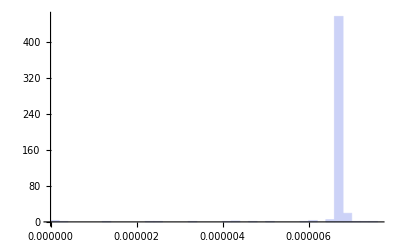

Generation = 9

Real = f(x)=x+x y+x^2 y+y^2+x^3 y^2

Best this generation = fitness=7.39798×10^-6 f(x,y)=-1-2 x^2+3 x^3+2 y+3 x y+7 x^2 y+x^3 y+2 y^2+5 x y^2+2 x^2 y^2-(2 x^2 y)/(-1-y+x/(y (x+y)))-(6 x^3 y)/(-1-y+x/(y (x+y)))-(4 x^2 y^2)/(-1-y+x/(y (x+y)))-(2 x^3 y^2)/(-1-y+x/(y (x+y)))

Best ever = Gen=7 fitness=7.81935×10^-6 f(x,y)=-(3 y)/2+y/x+x y+x^2 y-(5 y^2)/2+y^2/x-(3 x y^2)/2+y^3/2+y^3/x-2/(1+y)-1/(2 x^2 (1+y))+7/(4 x (1+y))-(7 x)/(2 (1+y))+x^2/(1+y)+x^3/(1+y)-3/(2 y (1+y))+1/(x y (1+y))+x/(y (1+y))+x^2/(y (1+y))+(23 y)/(4 (1+y))-y/(x^2 (1+y))+y/(x (1+y))-(13 x y)/(2 (1+y))-(5 x^2 y)/(2 (1+y))+(x^3 y)/(1+y)+(23 y^2)/(4 (1+y))-y^2/(2 x^2 (1+y))-(3 y^2)/(4 x (1+y))+(4 x y^2)/(1+y)-(3 x^2 y^2)/(2 (1+y))-(x^3 y^2)/(1+y)-(17 y^3)/(4 (1+y))-(5 y^3)/(2 x (1+y))+(3 x y^3)/(2 (1+y))+(3 x^2 y^3)/(2 (1+y))-y^4/(2 (1+y))+y^4/(2 x^2 (1+y))+(5 y^4)/(4 x (1+y))-(x y^4)/(2 (1+y))+(3 y^2)/(2 (-y+x (-1+x+y)))-y^2/(x (-y+x (-1+x+y)))-(x y^2)/(-y+x (-1+x+y))-(x^2 y^2)/(-y+x (-1+x+y))+(5 y^3)/(2 (-y+x (-1+x+y)))-y^3/(x (-y+x (-1+x+y)))+(3 x y^3)/(2 (-y+x (-1+x+y)))-y^4/(2 (-y+x (-1+x+y)))-y^4/(x (-y+x (-1+x+y)))+3/(2 (1+y) (-y+x (-1+x+y)))-1/(x (1+y) (-y+x (-1+x+y)))-x/((1+y) (-y+x (-1+x+y)))-x^2/((1+y) (-y+x (-1+x+y)))+(2 y)/((1+y) (-y+x (-1+x+y)))+y/(2 x^2 (1+y) (-y+x (-1+x+y)))-(7 y)/(4 x (1+y) (-y+x (-1+x+y)))+(7 x y)/(2 (1+y) (-y+x (-1+x+y)))-(x^2 y)/((1+y) (-y+x (-1+x+y)))-(x^3 y)/((1+y) (-y+x (-1+x+y)))-(23 y^2)/(4 (1+y) (-y+x (-1+x+y)))+y^2/(x^2 (1+y) (-y+x (-1+x+y)))-y^2/(x (1+y) (-y+x (-1+x+y)))+(13 x y^2)/(2 (1+y) (-y+x (-1+x+y)))+(5 x^2 y^2)/(2 (1+y) (-y+x (-1+x+y)))-(x^3 y^2)/((1+y) (-y+x (-1+x+y)))-(23 y^3)/(4 (1+y) (-y+x (-1+x+y)))+y^3/(2 x^2 (1+y) (-y+x (-1+x+y)))+(3 y^3)/(4 x (1+y) (-y+x (-1+x+y)))-(4 x y^3)/((1+y) (-y+x (-1+x+y)))+(3 x^2 y^3)/(2 (1+y) (-y+x (-1+x+y)))+(x^3 y^3)/((1+y) (-y+x (-1+x+y)))+(17 y^4)/(4 (1+y) (-y+x (-1+x+y)))+(5 y^4)/(2 x (1+y) (-y+x (-1+x+y)))-(3 x y^4)/(2 (1+y) (-y+x (-1+x+y)))-(3 x^2 y^4)/(2 (1+y) (-y+x (-1+x+y)))+y^5/(2 (1+y) (-y+x (-1+x+y)))-y^5/(2 x^2 (1+y) (-y+x (-1+x+y)))-(5 y^5)/(4 x (1+y) (-y+x (-1+x+y)))+(x y^5)/(2 (1+y) (-y+x (-1+x+y)))

Fitnesses =

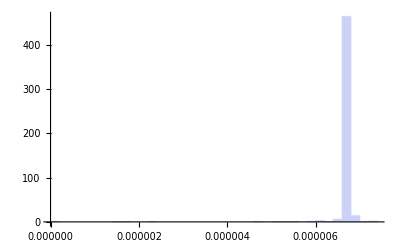

Generation = 10

Real = f(x)=x+x y+x^2 y+y^2+x^3 y^2

Best this generation = fitness=7.17821×10^-6 f(x,y)=-1+x+x^2+3 x^3+3 y+6 x y+3 x^2 y+6 y^2

Best ever = Gen=7 fitness=7.81935×10^-6 f(x,y)=-(3 y)/2+y/x+x y+x^2 y-(5 y^2)/2+y^2/x-(3 x y^2)/2+y^3/2+y^3/x-2/(1+y)-1/(2 x^2 (1+y))+7/(4 x (1+y))-(7 x)/(2 (1+y))+x^2/(1+y)+x^3/(1+y)-3/(2 y (1+y))+1/(x y (1+y))+x/(y (1+y))+x^2/(y (1+y))+(23 y)/(4 (1+y))-y/(x^2 (1+y))+y/(x (1+y))-(13 x y)/(2 (1+y))-(5 x^2 y)/(2 (1+y))+(x^3 y)/(1+y)+(23 y^2)/(4 (1+y))-y^2/(2 x^2 (1+y))-(3 y^2)/(4 x (1+y))+(4 x y^2)/(1+y)-(3 x^2 y^2)/(2 (1+y))-(x^3 y^2)/(1+y)-(17 y^3)/(4 (1+y))-(5 y^3)/(2 x (1+y))+(3 x y^3)/(2 (1+y))+(3 x^2 y^3)/(2 (1+y))-y^4/(2 (1+y))+y^4/(2 x^2 (1+y))+(5 y^4)/(4 x (1+y))-(x y^4)/(2 (1+y))+(3 y^2)/(2 (-y+x (-1+x+y)))-y^2/(x (-y+x (-1+x+y)))-(x y^2)/(-y+x (-1+x+y))-(x^2 y^2)/(-y+x (-1+x+y))+(5 y^3)/(2 (-y+x (-1+x+y)))-y^3/(x (-y+x (-1+x+y)))+(3 x y^3)/(2 (-y+x (-1+x+y)))-y^4/(2 (-y+x (-1+x+y)))-y^4/(x (-y+x (-1+x+y)))+3/(2 (1+y) (-y+x (-1+x+y)))-1/(x (1+y) (-y+x (-1+x+y)))-x/((1+y) (-y+x (-1+x+y)))-x^2/((1+y) (-y+x (-1+x+y)))+(2 y)/((1+y) (-y+x (-1+x+y)))+y/(2 x^2 (1+y) (-y+x (-1+x+y)))-(7 y)/(4 x (1+y) (-y+x (-1+x+y)))+(7 x y)/(2 (1+y) (-y+x (-1+x+y)))-(x^2 y)/((1+y) (-y+x (-1+x+y)))-(x^3 y)/((1+y) (-y+x (-1+x+y)))-(23 y^2)/(4 (1+y) (-y+x (-1+x+y)))+y^2/(x^2 (1+y) (-y+x (-1+x+y)))-y^2/(x (1+y) (-y+x (-1+x+y)))+(13 x y^2)/(2 (1+y) (-y+x (-1+x+y)))+(5 x^2 y^2)/(2 (1+y) (-y+x (-1+x+y)))-(x^3 y^2)/((1+y) (-y+x (-1+x+y)))-(23 y^3)/(4 (1+y) (-y+x (-1+x+y)))+y^3/(2 x^2 (1+y) (-y+x (-1+x+y)))+(3 y^3)/(4 x (1+y) (-y+x (-1+x+y)))-(4 x y^3)/((1+y) (-y+x (-1+x+y)))+(3 x^2 y^3)/(2 (1+y) (-y+x (-1+x+y)))+(x^3 y^3)/((1+y) (-y+x (-1+x+y)))+(17 y^4)/(4 (1+y) (-y+x (-1+x+y)))+(5 y^4)/(2 x (1+y) (-y+x (-1+x+y)))-(3 x y^4)/(2 (1+y) (-y+x (-1+x+y)))-(3 x^2 y^4)/(2 (1+y) (-y+x (-1+x+y)))+y^5/(2 (1+y) (-y+x (-1+x+y)))-y^5/(2 x^2 (1+y) (-y+x (-1+x+y)))-(5 y^5)/(4 x (1+y) (-y+x (-1+x+y)))+(x y^5)/(2 (1+y) (-y+x (-1+x+y)))

Fitnesses =

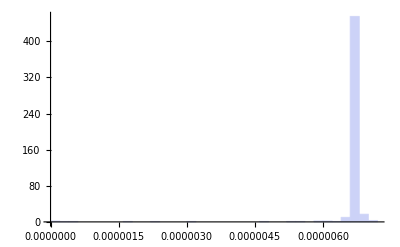

Generation = 11

Real = f(x)=x+x y+x^2 y+y^2+x^3 y^2

Divide::indet: Indeterminate expression 0/0 encountered.

Best this generation = fitness=0.0000211732 f(x,y)=Indeterminate

Best ever = Gen=7 fitness=7.81935×10^-6 f(x,y)=-(3 y)/2+y/x+x y+x^2 y-(5 y^2)/2+y^2/x-(3 x y^2)/2+y^3/2+y^3/x-2/(1+y)-1/(2 x^2 (1+y))+7/(4 x (1+y))-(7 x)/(2 (1+y))+x^2/(1+y)+x^3/(1+y)-3/(2 y (1+y))+1/(x y (1+y))+x/(y (1+y))+x^2/(y (1+y))+(23 y)/(4 (1+y))-y/(x^2 (1+y))+y/(x (1+y))-(13 x y)/(2 (1+y))-(5 x^2 y)/(2 (1+y))+(x^3 y)/(1+y)+(23 y^2)/(4 (1+y))-y^2/(2 x^2 (1+y))-(3 y^2)/(4 x (1+y))+(4 x y^2)/(1+y)-(3 x^2 y^2)/(2 (1+y))-(x^3 y^2)/(1+y)-(17 y^3)/(4 (1+y))-(5 y^3)/(2 x (1+y))+(3 x y^3)/(2 (1+y))+(3 x^2 y^3)/(2 (1+y))-y^4/(2 (1+y))+y^4/(2 x^2 (1+y))+(5 y^4)/(4 x (1+y))-(x y^4)/(2 (1+y))+(3 y^2)/(2 (-y+x (-1+x+y)))-y^2/(x (-y+x (-1+x+y)))-(x y^2)/(-y+x (-1+x+y))-(x^2 y^2)/(-y+x (-1+x+y))+(5 y^3)/(2 (-y+x (-1+x+y)))-y^3/(x (-y+x (-1+x+y)))+(3 x y^3)/(2 (-y+x (-1+x+y)))-y^4/(2 (-y+x (-1+x+y)))-y^4/(x (-y+x (-1+x+y)))+3/(2 (1+y) (-y+x (-1+x+y)))-1/(x (1+y) (-y+x (-1+x+y)))-x/((1+y) (-y+x (-1+x+y)))-x^2/((1+y) (-y+x (-1+x+y)))+(2 y)/((1+y) (-y+x (-1+x+y)))+y/(2 x^2 (1+y) (-y+x (-1+x+y)))-(7 y)/(4 x (1+y) (-y+x (-1+x+y)))+(7 x y)/(2 (1+y) (-y+x (-1+x+y)))-(x^2 y)/((1+y) (-y+x (-1+x+y)))-(x^3 y)/((1+y) (-y+x (-1+x+y)))-(23 y^2)/(4 (1+y) (-y+x (-1+x+y)))+y^2/(x^2 (1+y) (-y+x (-1+x+y)))-y^2/(x (1+y) (-y+x (-1+x+y)))+(13 x y^2)/(2 (1+y) (-y+x (-1+x+y)))+(5 x^2 y^2)/(2 (1+y) (-y+x (-1+x+y)))-(x^3 y^2)/((1+y) (-y+x (-1+x+y)))-(23 y^3)/(4 (1+y) (-y+x (-1+x+y)))+y^3/(2 x^2 (1+y) (-y+x (-1+x+y)))+(3 y^3)/(4 x (1+y) (-y+x (-1+x+y)))-(4 x y^3)/((1+y) (-y+x (-1+x+y)))+(3 x^2 y^3)/(2 (1+y) (-y+x (-1+x+y)))+(x^3 y^3)/((1+y) (-y+x (-1+x+y)))+(17 y^4)/(4 (1+y) (-y+x (-1+x+y)))+(5 y^4)/(2 x (1+y) (-y+x (-1+x+y)))-(3 x y^4)/(2 (1+y) (-y+x (-1+x+y)))-(3 x^2 y^4)/(2 (1+y) (-y+x (-1+x+y)))+y^5/(2 (1+y) (-y+x (-1+x+y)))-y^5/(2 x^2 (1+y) (-y+x (-1+x+y)))-(5 y^5)/(4 x (1+y) (-y+x (-1+x+y)))+(x y^5)/(2 (1+y) (-y+x (-1+x+y)))

Fitnesses =

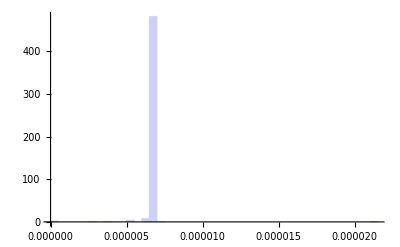

Generation = 12

$Aborted

```mathematica
keeprunning=True;
While[keeprunning==True,
myCurrentGen=myCurrentGen+1;
Print["Generation = ",myCurrentGen];
(*Print[Button["End Loop",keeprunning=False; Print["Forcing stop after this loop"]]];*)
myNextGenList=RandomChoice[myPreviousGenFitness->myPreviousGenList,myGenSize];
myNextGenList=Join[RandomChoice[myPreviousGenFitness->myPreviousGenList,Floor[2*myGenSize/5]],RandomSample[myPreviousGenFitness->myPreviousGenList,Floor[1*myGenSize/5]],RandomSample[myPreviousGenFitness->myPreviousGenList,Floor[1*myGenSize/5]]];
myNextGenList=Join[myNextGenList,RandomChoice[myPreviousGenList,Length[myPreviousGenList]-Length[myNextGenList]]];
myNextGenList=BreedNodeList[myNextGenList, myCrossoverProbability,myRegrowProbability,myPointProbability,myMaxComplexity,myMaxInitDepth];
myNextGen=Map[ListToNode,myNextGenList];
myNextGenFitness=CalculateFitness[myTestFunction,myNextGen];
myNextGenBestPosition=Ordering[myNextGenFitness,-1][[1]];
Print["Real = f(x)=",Expand[TargetFunction[x,y]]];
Print["Best this generation = ","fitness=",myNextGenFitness[[myNextGenBestPosition]]," f(x,y)=",Expand[myNextGen[[myNextGenBestPosition]]/.DisplayTranslation]];
(*Show[ListPlot3D[DataPoints,Mesh->All],Plot3D[(myNextGen[[myNextGenBestPosition]]/.FunctionTranslation/.{x->xvar,y->yvar}),{xvar,-10,10},{yvar,-10,10},Mesh->None]]*)
Print["Best ever = ","Gen=",myBestFind[[1]]," fitness=",myBestFind[[2]]," f(x,y)=",Expand[myBestFind[[3]]/.DisplayTranslation]];
(*Show[ListPlot3D[DataPoints,Mesh->All],Plot3D[(myBestFind[[3]]/.FunctionTranslation/.{x->xvar,y->yvar}),{xvar,-10,10},{yvar,-10,10},Mesh->None]]*)
Print["Fitnesses = "];
Print[Histogram[myNextGenFitness]];
If[myNextGenFitness[[myNextGenBestPosition]]>myBestFind[[2]],myBestFind={myCurrentGen,myNextGenFitness[[myNextGenBestPosition]],myNextGen[[myNextGenBestPosition]]}];
myPreviousGenList=myNextGenList;
myPreviousGenFitness=myNextGenFitness;
If[myBestFind[[2]]>myMinSolutionFitness,keeprunning=False;Print["Found a solution with fitness > ",myMinSolutionFitness];Print["fitness = ",myBestFind[[2]],"; gen = ",myBestFind[[1]],"; f(x,y) = ", myBestFind[[3]]/.DisplayTranslation]];
]
```